## Three Harmonic Oscillators

## December 11, 2025

### Three Oscillators — Formulas for the Accelerations

Three equal masses connected to each other and the walls by six identical springs, we have:

a_1=-ω_0^2 x_1+ω_0^2(x_2-x_1)

a_2=-ω_0^2(x_2-x_1)+ω_0^2(x_3-x_2)
 
a_3=-ω_0^2(x_3-x_2)+ω_0^2(-x_3)

where

ω_0^2≡k/m

### Why Stop at Three? — Formulas for the Accelerations of Many Oscillators

Let’s have n masses and n+1 springs. Let’s do n=3, but later on, we can make n whatever we like. Let’s also define ω_0 while we are at it:

```mathematica
n=3;
omega0=2Pi;
```

We need to handle the left-most and right-most oscillators (the ones that are next to the walls) specially. That’s going to require some If[] statements:

```mathematica
acceleration[j_,allPositions_]:=
-omega0^2(allPositions[[j]]-If[j==1, 0, allPositions[[j-1]]])+omega0^2(If[j==n,0,allPositions[[j+1]]]-allPositions[[j]])
```

### Initial Conditions

First set up the duration. Let’s also define steps and deltaT while we are at it::

```mathematica
tInitial = 0.0;
tFinal = 10.0;
steps = 2000;
deltaT = (tFinal - tInitial)/steps;
```

#### Cool Initial Conditions, but Ignore them for Now

Here are three sets of initial conditions (these are known as eigenvectors and the omegas are known as eigenvalues) that are very particular to the case n=3:

```mathematica
iA3={
{1/2,1/Sqrt[2],1/2},
{-1/Sqrt[2],0,1/Sqrt[2]},
{1/2,-1/Sqrt[2],1/2}
};
omega3={Sqrt[2-Sqrt[2]],Sqrt[2],Sqrt[2+Sqrt[2]]}omega0;
```

#### Simple-Minded Initial Conditions

For now, just implement these more simple-minded initial condition:

```mathematica
pluck=-0.5;
(* Make pluck the first mass's displacement and all the others zero. *)
initialPositions={pluck,0.0,0.0};
(* Make all the initial velocities zero *)
initialVelocities=Table[0.0,n];
```

#### Try Changing the Initial Conditions

Go back up to the initial conditions section, and where it said,

initialPositions={-pluck, 0.0, 0.0};

change that line to one of the special initial conditions:

initialPositions=iA3[[1]];
initialPositions=iA3[[2]];
initialPositions=iA3[[3]];

All of these are interesting!

```mathematica
initialPositions=iA3[[3]];
```

We have a decision to make on how we are packing the time, the positions, and the velocities into the initial conditions list, but here is the obvious choice:

```mathematica
initialConditions={tInitial,initialPositions,initialVelocities};
```

In particular, initialPositions and initialVelocities are lists, so the list we have just created contains lists!

### Second-Order Runge-Kutta — Formulas for n Particles

t_(i+1)=t_i+Δt

x_j^*=x_j(t_i)+v_j(t_i)·Δt/2       (j goes from 1 to n)

v_j(t_(i+1))=v_j(t_i)+a_j(that depends on neighboring x^* — see formulas for the accelerations above)·Δt

x_j(t_(i+1))=x_j(t_i)+ (v_j(t_i)+v_j(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementation

Your turn to put it all together into the real thing:

```mathematica
rungeKutta2[cc_]:= (
curTime=cc[[1]];
curPositions=cc[[2]];
curVelocities=cc[[3]];
newTime=curTime+deltaT;
positionsStar=curPositions+curVelocities deltaT/2;
accelerations=acceleration[#,positionsStar]&/@Range[n];
newVelocities=curVelocities+accelerations deltaT;
newPositions=curPositions+(curVelocities+newVelocities)deltaT/2;
{newTime,newPositions,newVelocities}
)
(* Test your implementation on the initial conditions *)
N[rungeKutta2[initialConditions]]
(* This is what I get: *)
(* {0.005, {-0.00024674, -0.499507, -0.00024674, 0., 0.}, {-0.098696, 0.197392, -0.098696, 0., 0.}} *)
```

{0.005,{0.499158,-0.705915,0.499158},{-0.336969,0.476547,-0.336969}}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
rk2ResultsTransposed=Transpose[rk2Results];
positionLists=rk2ResultsTransposed[[2]];
```

#### A Graphic

The graphics work is straightforward but a little time-consuming, and not terribly instructive, so it is already all done:

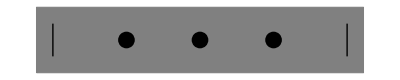

```mathematica
coupledOscillatorGraphic[positionList_]:=Graphics[{
width=10;
buffer=0.5;
netWidth=width-2 buffer;
wallHeight=1.0;
numberOfSprings=n+1;
(* the next line makes a gray rectangle *)
{EdgeForm[Thin],Gray,Polygon[{{0,-1},{width,-1},{width,1},{0,1}}]},
(* the next two lines make the walls *)
Line[{{buffer,-wallHeight/2},{buffer,wallHeight/2}}],
Line[{{width-buffer,-wallHeight/2},{width-buffer,wallHeight/2}}],
(* finally we draw all the points *)
Table[Style[Point[{positionList[[j]]+netWidth/numberOfSprings j+buffer,0.0}],PointSize[0.03]],{j,n}]
}]
(* A little test to see if our code at least draws equally-spaced points when the positions are all zero: *)
coupledOscillatorGraphic[Table[0.0,n]]
```

#### Animating The Graphics

```mathematica
Animate[coupledOscillatorGraphic[positionLists[[i]]],{i,1,steps,1}, DefaultDuration->tFinal-tInitial]
```